```mathematica
(*このファイルのコードでは有限要素法により拡散方程式を説いた結果の剛性行列から隣接行列を差癖する*)
```

```mathematica
(*ランダムな多角形の生成*)
(*listRegion=RandomPolygon[Random[Integer,{1000,1000}],2];*)
listRegion=RandomPolygon[20,100];
(*Region[#,Frame->True]&/@listRegion;*)
```

```mathematica
(*シミュレーション(一括)*)
(*要素数はMaxCellMeasureを変えてもあまり変わらないので固定する*)

Needs["NDSolve`FEM`"]
SetDirectory[NotebookDirectory[]];

(*Fixed parameters*)
cellSize=0.01;
testRate=0.2;
t=20;
nBeads=100;

ParallelTable[
Ω=listRegion[[i]];
maxcellsize=cellSize;

nr=ToElementMesh[#,MaxCellMeasure->maxcellsize]&@BoundaryDiscretizeRegion@Ω;

vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y,z}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[3]}},"DampingCoefficients"->{{1}}};
initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];

(*e-^tMを隣接行列とみなす場合は要素の頂点数と同じ数の種類のビーズを使うことを仮定している*)
(*次元が大きいと行列の指数関数を計算するのが大変なので用いたビーズの種類に次元を縮める*)
n=Length@stiffness;  (*要素数*)
(*節点のインデックス(1~n)を重複のないように用いるビーズの数だけランダムに選ぶ*)
iInitialPoints=RandomSample[Range[n],nBeads];
(*ビーズの座標、つまり最初に各ビーズをおく節点の座標*)
coBeads=nr["Coordinates"][[iInitialPoints]];
V=Table[UnitVector[n,iInitialPoints[[iBead]]],{iBead,nBeads}];
R=Chop@MatrixExp[t*stiffness,#]&/@V;
(*真の隣接行列*)
M=R.Transpose[R];
(*隣接行列0より小さい要素をの0に置き換える*)
adjMat=M/.x_/;x<0->0;
(*Export adjacency matrices*)
Export[
(*"adj_mat/shape:"<>ToString[i]<>"beads:"<>Tostring<>"_t="<>ToString[t]<>".mtx",*)
ToString/@{"adj_mat/shape:",i,"_beads:",nBeads,"_time:",t,".mtx"}//StringJoin,
SparseArray@adjMat
];
(*Export coordinates of beads for a shape as a CSV file?*)
Export[
ToString/@{"beads_coord/shape:",i,"_beads:",nBeads,"_time:",t,".csv"}//StringJoin,
coBeads
],
{i,Range@Length@listRegion}(*,{nBeads,{100,500,1000,2000}},{t,{10,20,30,40,50,60}}*)
]
```

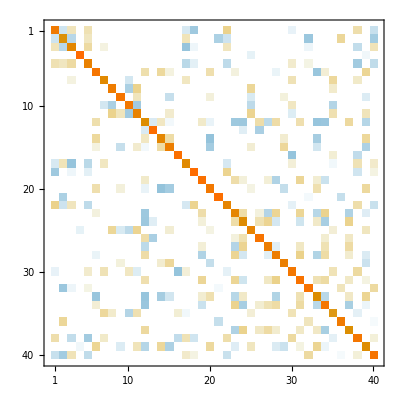

{28292,28292}

```mathematica
(*1種類でのテスト*)
Needs["NDSolve`FEM`"]
SetDirectory[NotebookDirectory[]];

Ω=listRegion[[1]];
maxcellsize=.4;
(*ϵ=0*0.001;
τ=0.1;*)
nr=ToElementMesh[#,MaxCellMeasure->0.1]&@BoundaryDiscretizeRegion[Ω];

vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y,z}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[3]}},"DampingCoefficients"->{{1}}};
initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];

n=Length@stiffness;
V=Table[UnitVector[n,RandomInteger[{1,n}]],{40}];
Dimensions@V
R=Chop@MatrixExp[.2*stiffness,#]&/@V;
Dimensions@R
Dimensions@Transpose@R
M=R.Transpose[R]
MatrixPlot@M
am=M/.x_/;x<0->0;
Export["stiffTest.mtx",SparseArray[am]];
Dimensions@stiffness
```

```mathematica
n=Length@stiffness;
V=Table[UnitVector[n,RandomInteger[{1,n}]],{40}];
Dimensions@V
R=Chop@MatrixExp[.2*stiffness,#]&/@V;
Dimensions@R
Dimensions@Transpose@R
M=R.Transpose[R]
MatrixPlot@M
```